```mathematica
dat = Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\jule\\2\\2jule_2acc.dat"];
```

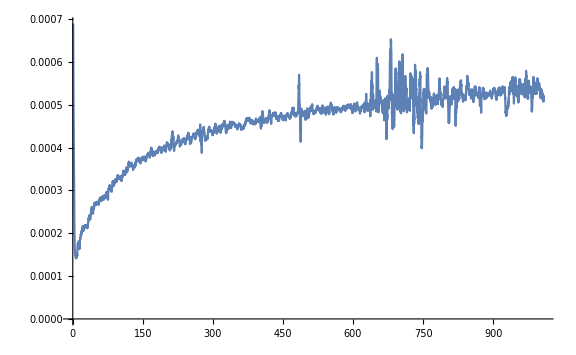

```mathematica
ListLinePlot[MeanFilter[dat[[All,{3,2}]],{10,0}],ImageSize->Large,PlotRange->All]
```

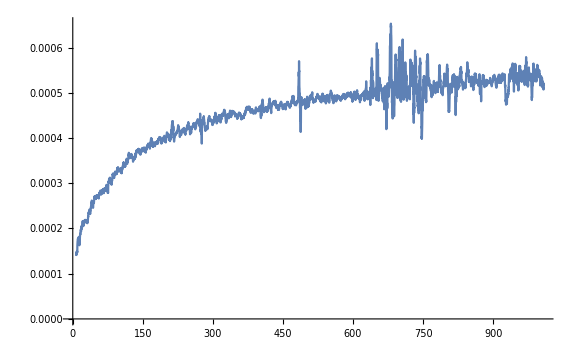

```mathematica
ListLinePlot[MeanFilter[dat[[40;;,{3,2}]],{10,0}],ImageSize->Large,PlotRange->All]
```

```mathematica
coef = FindFit[MeanFilter[dat[[40;;,{3,2}]],{20,0}],{c-a*Exp[-r x]-b Exp[-k x]},{c,a,r,b,k},x]
```

{c→0.000554887,a→0.000183106,r→0.0160763,b→0.000237474,k→0.00241568}

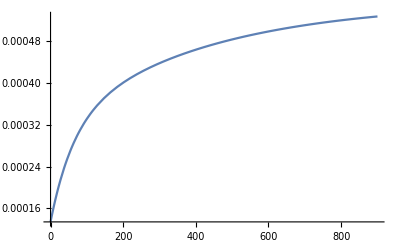

```mathematica
Plot[(c-a*Exp[-r x]-b Exp[-k x])/.coef,{x,0,900}]
```

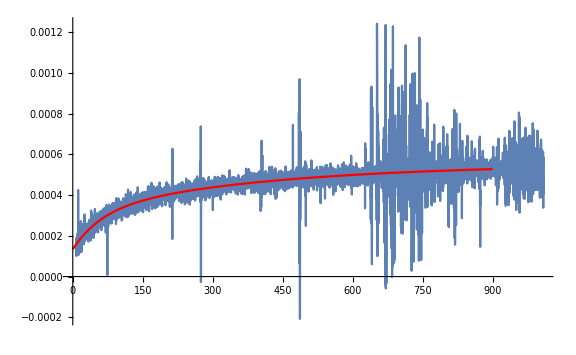

```mathematica
Show[
ListLinePlot[MeanFilter[dat[[40;;,{3,2}]],{0,0}],ImageSize->Large,PlotRange->All],
Plot[(c-a*Exp[-r x]-b*Exp[-k x])/.coef,{x,0,900},PlotStyle->Red]
]
```